```mathematica
Needs["Cosmology`"]
```

```mathematica
Convert[HubbleConstant, 1/Second]
```

3.24077928966×10^-18 Second^-1

## Initialization

```mathematica
(* Switch to the directory the notebook and data files are in *)
SetDirectory[NotebookDirectory[]]
```

/Users/npadmana/myWork/np_sandbox/diff_transfer_fn

```mathematica
(* Number of files *)
```

```mathematica
nfiles = 5;
```

```mathematica
(* zvals -- hardcoded is not ideal, but why not?? *)
```

```mathematica
zvals= {0.04, 0.03, 0.02, 0.01, 0.00};
```

```mathematica
(* Set the file name list *)
```

```mathematica
fnames = "test_transfer_z"<>ToString[#]<>".dat"& /@ Range[0,nfiles-1];
```

```mathematica
(* Read in all the files *)
```

```mathematica
tData = Import[#, "Table"] & /@ fnames;
```

```mathematica
Dimensions[tData]
```

{5,692,7}

```mathematica
kval = tData[[1,All,1]];
```

```mathematica
transfers = tData[[All, All, {2,3}]];
```

```mathematica
Dimensions[transfers]
```

{5,692,2}

### Normalization

The CAMB transfer functions are normalized to make it easy to compute power spectra, but this is inconvenient when computing derivatives of transfer functions. So let us remove and store the normalizations. I

```mathematica
norms = transfers[[All, 1, All]]
```

{{1.99711×10^7,1.99711×10^7},{2.00696×10^7,2.00696×10^7},{2.01684×10^7,2.01684×10^7},{2.02675×10^7,2.02675×10^7},{2.03668×10^7,2.03668×10^7}}

```mathematica
Dimensions[norms]
```

{5,2}

```mathematica
transfer1 = Transpose[ Transpose[transfers, {1,3,2}]/norms, {1,3,2}];
```

```mathematica
transfer1 = transfers;
```

```mathematica
transfer1[[All, 1;;10, All]]
```

{{{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.}},{{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.}},{{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.}},{{1.,1.},{1.,1.},{1.,1.},{1.,1.},{0.999995,0.999995},{0.999995,0.999995},{0.999995,0.999995},{0.999995,0.999995},{0.999995,0.999995},{0.999995,0.999995}},{{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.}}}

```mathematica
Dimensions[transfer1]
```

{5,692,2}

```mathematica
tNorm1 = transfer1[[All,All,2]]- transfer1[[All,All,1]];
```

```mathematica
tNorm = GaussianFilter[tNorm1[[#,All]], 5] & /@ Range[5];
```

```mathematica
Dimensions[tNorm]
```

{5,692}

```mathematica
(* We can do this more cleverly, by precomputing coefficients, but not today *)
```

```mathematica
D[Fit[Thread[{zvals, tNorm[[All,201]]}], {1, z}, z],z] /. z->0
```

-1.95002×10^-6

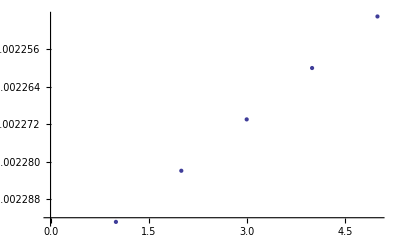

```mathematica
ListPlot[tNorm[[All, 400]]]
```

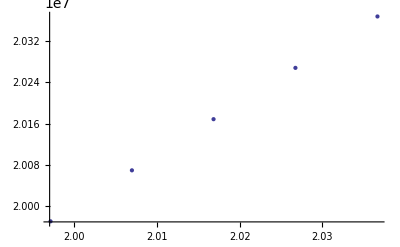

```mathematica
ListPlot[norms]
```

```mathematica
(* This derivative is wrt z, we want the derivative wrt t *)
```

```mathematica
z[t_] := 1/a[t] - 1;
```

```mathematica
D[z[t], t]
```

-a'[t]/a[t]^2

```mathematica
(* This is nothing but the Hubble constant divided by the scale factor, which for z=0 is 1 *)
(* However looking ahead the only thing we need are dimensionless values so lets drop this for now *)
```

```mathematica
tBaryDot=D[Fit[Thread[{zvals, tNorm1[[All,#]]}], {1, z}, z],z]/.z->0 & /@ Range[Dimensions[tNorm1][[2]]];
```

```mathematica
Dimensions[tBaryDot]
```

{692}

```mathematica
tBaryDot[[400]]
```

-0.00109765

```mathematica
kval[[400]]
```

0.0296046

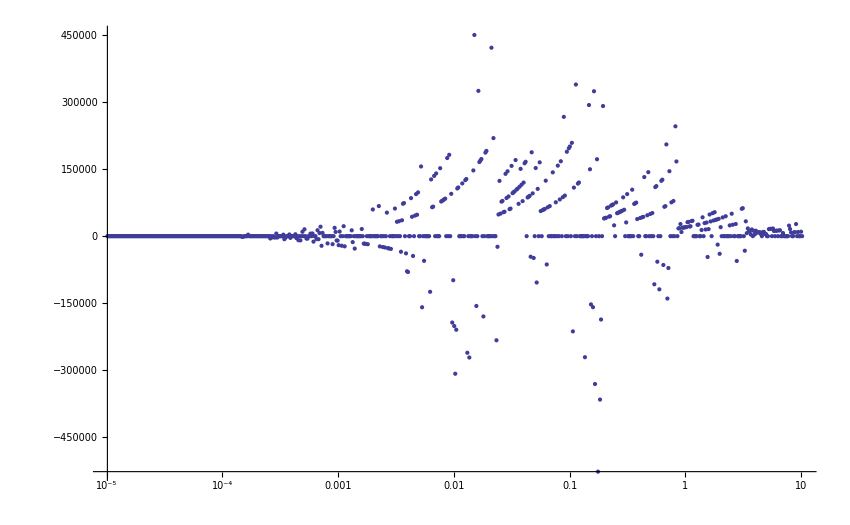

```mathematica
ListLogLinearPlot[Thread[{kval, tBaryDot*kval*1*^4}], PlotRange->Full]
```

```mathematica
kval[[200;;220]]
```

{0.000542228,0.000553181,0.000564356,0.000575757,0.000587388,0.000599254,0.00061136,0.00062371,0.00063631,0.000649164,0.000662278,0.000675657,0.000689306,0.000703231,0.000717437,0.000731931,0.000746717,0.000761801,0.000777191,0.000792891,0.000808909}

```mathematica
tBaryDot[[218;;222]]*1*^4
```

{-0.0243221,-0.0243221,-1.00631,-0.0243221,-0.0243221}

```mathematica
tNorm[[All,219]]
```

{-5.00724×10^-6,-4.98266×10^-6,-4.95825×10^-6,-4.93401×10^-6,-4.90995×10^-6}

```mathematica
Fit[Thread[{{4.,3.,2.,1.,0.}, tNorm[[All,219]]}],{1,z},z]
```

-4.90978×10^-6-2.43221×10^-8 z

```mathematica
tNorm[[All, 220]]
```

{-5.00724×10^-6,-4.98266×10^-6,-4.95825×10^-6,-4.93401×10^-6,0.}

```mathematica
tNorm[[All,221]]
```

{-5.00724×10^-6,-4.98266×10^-6,-4.95825×10^-6,-4.93401×10^-6,-4.90995×10^-6}

```mathematica
GaussianFilter[tNorm[[4]],5][[398;;402]]
```

{-0.00221743,-0.00223994,-0.00226001,-0.00227745,-0.00229208}

```mathematica
tNorm[[4,398;;402]]
```

{-0.00222326,-0.00224645,-0.00226668,-0.00228445,-0.00229974}